## Question 8: Mohamed Gas

x^2+xy+y^2=3
dy/dx=dy/dx(x^2+xy+y^2)=dy/dx(3)
=2x+(1*y+x*1*dy/dx)+2y*dy/dx=dy/dx(3)
=2x+y+x*dy/dx+2y*dy/dx=0
=2x+y+dy/dx(x+2y)=0
dy/dx=(-2x-y)/(x+2y)

m=dy/dx
dy/dx=(-2(1)-(-2))/(1-4)
m=0


Equation of Tangent Line
y-(-2)=0(x-1)
y=-2

Equation of Normal Line

y=-1/0(x-1)-2

```mathematica
points=ListLinePlot[{{1, -2}, {1, 5}}, PlotLegends->{"y=-1/0(x-1)-2 : Normal Line "},PlotStyle->{Black,Thick}];
```

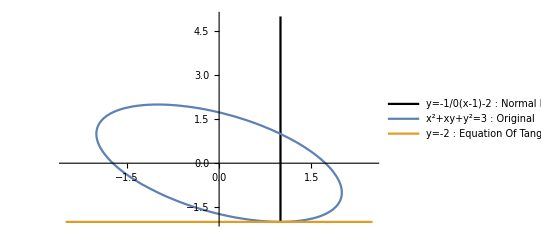

```mathematica
graph=ContourPlot[{x^2 + x*y + y^2 == 3,y==-2}, {x, -2.5, 2.5}, {y, -4., 4.},Frame->None,Axes->True,PlotLegends->{"x^2+xy+y^2=3 : Original","y=-2  : Equation Of TangentLIne"}];
 Show[{points,graph},PlotRange->All]
```